## Exercise 1 solutions (with new section illustrating Newton’s method) Toby Wiseman (Imperial College) Mathematica Summer School, Porto 2014

```mathematica
NX=6;

NY=6;
```

## Problem 1 : create the basic domain

```mathematica
array={};

boundary={};interior={};

count=1;

count1=1;

count2=1;

Do[
If[x==1,
AppendTo[boundary,count++];
AppendTo[array,{{x,y},ToExpression["b"<>ToString[count1++]]}];,
AppendTo[interior,count++];
AppendTo[array,{{x,y},ToExpression["f"<>ToString[count2++]]}];
]
,{x,1,NX},{y,1,NY}];

grid=Function[{{(#1[[1]]-1.)/(NX-0.5),2π(#1[[2]]-0.5)/(NY)},#2}]@@@array;
```

```mathematica
array
```

{{{1,1},b1},{{1,2},b2},{{1,3},b3},{{1,4},b4},{{1,5},b5},{{1,6},b6},{{2,1},f1},{{2,2},f2},{{2,3},f3},{{2,4},f4},{{2,5},f5},{{2,6},f6},{{3,1},f7},{{3,2},f8},{{3,3},f9},{{3,4},f10},{{3,5},f11},{{3,6},f12},{{4,1},f13},{{4,2},f14},{{4,3},f15},{{4,4},f16},{{4,5},f17},{{4,6},f18},{{5,1},f19},{{5,2},f20},{{5,3},f21},{{5,4},f22},{{5,5},f23},{{5,6},f24},{{6,1},f25},{{6,2},f26},{{6,3},f27},{{6,4},f28},{{6,5},f29},{{6,6},f30}}

```mathematica
grid//MatrixForm
```

({0.,0.523599} | b1
{0.,1.5708} | b2
{0.,2.61799} | b3
{0.,3.66519} | b4
{0.,4.71239} | b5
{0.,5.75959} | b6
{0.181818,0.523599} | f1
{0.181818,1.5708} | f2
{0.181818,2.61799} | f3
{0.181818,3.66519} | f4
{0.181818,4.71239} | f5
{0.181818,5.75959} | f6
{0.363636,0.523599} | f7
{0.363636,1.5708} | f8
{0.363636,2.61799} | f9
{0.363636,3.66519} | f10
{0.363636,4.71239} | f11
{0.363636,5.75959} | f12
{0.545455,0.523599} | f13
{0.545455,1.5708} | f14
{0.545455,2.61799} | f15
{0.545455,3.66519} | f16
{0.545455,4.71239} | f17
{0.545455,5.75959} | f18
{0.727273,0.523599} | f19
{0.727273,1.5708} | f20
{0.727273,2.61799} | f21
{0.727273,3.66519} | f22
{0.727273,4.71239} | f23
{0.727273,5.75959} | f24
{0.909091,0.523599} | f25
{0.909091,1.5708} | f26
{0.909091,2.61799} | f27
{0.909091,3.66519} | f28
{0.909091,4.71239} | f29
{0.909091,5.75959} | f30)

```mathematica
boundary

Print["For example; ",grid[[boundary[[2]]]]];
```

{1,2,3,4,5,6}

For example; {{0.,1.5708},b2}

```mathematica
interior

Print["For example; ",grid[[interior[[2]]]]];
```

{7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36}

For example; {{0.181818,1.5708},f2}

Notes;

For future convenience I will also create a list of the boundary variables and the interior variables, together with a combined list of all variables.

```mathematica
boundaryvar=Table[ToExpression["b"<>ToString[ii]],{ii,1,count1-1}]
```

{b1,b2,b3,b4,b5,b6}

```mathematica
interiorvar=Table[ToExpression["f"<>ToString[ii]],{ii,1,count2-1}]
```

{f1,f2,f3,f4,f5,f6,f7,f8,f9,f10,f11,f12,f13,f14,f15,f16,f17,f18,f19,f20,f21,f22,f23,f24,f25,f26,f27,f28,f29,f30}

```mathematica
variables=Join[boundaryvar,interiorvar]
```

{b1,b2,b3,b4,b5,b6,f1,f2,f3,f4,f5,f6,f7,f8,f9,f10,f11,f12,f13,f14,f15,f16,f17,f18,f19,f20,f21,f22,f23,f24,f25,f26,f27,f28,f29,f30}

Also create ' size' variable to store length of grid list;

```mathematica
size=Length[grid]
```

36

Likewise for future convenience create size variables for the boundary and interior lists;

```mathematica
sizeboundary=Length[boundary]

sizeinterior=Length[interior]
```

6

30

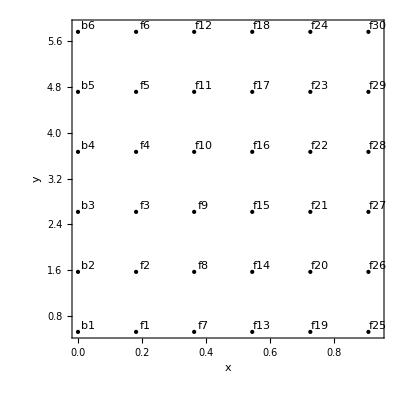

```mathematica
p1=Show[Graphics[Table[Point[grid[[ii,1]]],{ii,1,size}]],PlotRange->All,AspectRatio->1];

p2=Show[Graphics[Table[Text[grid[[ii,2]],{0.03,0.1}+grid[[ii,1]]],{ii,1,size}]],PlotRange->All,AspectRatio->1];

Show[p1,p2,Frame->True,FrameLabel->{"x","y"}]
```

## Problem 2 : create an extended domain to implement reflection and periodic boundary conditions

```mathematica
tmp=DeleteDuplicates[grid[[All,1,1]]]
```

{0.,0.181818,0.363636,0.545455,0.727273,0.909091}

```mathematica
Join[tmp,2-Reverse[tmp]]
```

{0.,0.181818,0.363636,0.545455,0.727273,0.909091,1.09091,1.27273,1.45455,1.63636,1.81818,2.}

Firstly double the grid in x to implement reflection boundary condition about x = 1;

```mathematica
griddouble=Join[grid,Function[{{2-#1[[1]],#1[[2]]},#2}]@@@grid];
```

```mathematica
MatrixForm[griddouble]
```

({0.,0.523599} | b1
{0.,1.5708} | b2
{0.,2.61799} | b3
{0.,3.66519} | b4
{0.,4.71239} | b5
{0.,5.75959} | b6
{0.181818,0.523599} | f1
{0.181818,1.5708} | f2
{0.181818,2.61799} | f3
{0.181818,3.66519} | f4
{0.181818,4.71239} | f5
{0.181818,5.75959} | f6
{0.363636,0.523599} | f7
{0.363636,1.5708} | f8
{0.363636,2.61799} | f9
{0.363636,3.66519} | f10
{0.363636,4.71239} | f11
{0.363636,5.75959} | f12
{0.545455,0.523599} | f13
{0.545455,1.5708} | f14
{0.545455,2.61799} | f15
{0.545455,3.66519} | f16
{0.545455,4.71239} | f17
{0.545455,5.75959} | f18
{0.727273,0.523599} | f19
{0.727273,1.5708} | f20
{0.727273,2.61799} | f21
{0.727273,3.66519} | f22
{0.727273,4.71239} | f23
{0.727273,5.75959} | f24
{0.909091,0.523599} | f25
{0.909091,1.5708} | f26
{0.909091,2.61799} | f27
{0.909091,3.66519} | f28
{0.909091,4.71239} | f29
{0.909091,5.75959} | f30
{2.,0.523599} | b1
{2.,1.5708} | b2
{2.,2.61799} | b3
{2.,3.66519} | b4
{2.,4.71239} | b5
{2.,5.75959} | b6
{1.81818,0.523599} | f1
{1.81818,1.5708} | f2
{1.81818,2.61799} | f3
{1.81818,3.66519} | f4
{1.81818,4.71239} | f5
{1.81818,5.75959} | f6
{1.63636,0.523599} | f7
{1.63636,1.5708} | f8
{1.63636,2.61799} | f9
{1.63636,3.66519} | f10
{1.63636,4.71239} | f11
{1.63636,5.75959} | f12
{1.45455,0.523599} | f13
{1.45455,1.5708} | f14
{1.45455,2.61799} | f15
{1.45455,3.66519} | f16
{1.45455,4.71239} | f17
{1.45455,5.75959} | f18
{1.27273,0.523599} | f19
{1.27273,1.5708} | f20
{1.27273,2.61799} | f21
{1.27273,3.66519} | f22
{1.27273,4.71239} | f23
{1.27273,5.75959} | f24
{1.09091,0.523599} | f25
{1.09091,1.5708} | f26
{1.09091,2.61799} | f27
{1.09091,3.66519} | f28
{1.09091,4.71239} | f29
{1.09091,5.75959} | f30)

Secondly put a copy of the grid at y = 0 and y = 2 π to implement periodicity in y;

```mathematica
gridfull=Join[Function[{{#1[[1]],#1[[2]]-2π},#2}]@@@griddouble,griddouble,Function[{{#1[[1]],#1[[2]]+2π},#2}]@@@griddouble];
```

```mathematica
gridfull
```

{{{0.,-5.75959},b1},{{0.,-4.71239},b2},{{0.,-3.66519},b3},{{0.,-2.61799},b4},{{0.,-1.5708},b5},{{0.,-0.523599},b6},{{0.181818,-5.75959},f1},{{0.181818,-4.71239},f2},{{0.181818,-3.66519},f3},{{0.181818,-2.61799},f4},{{0.181818,-1.5708},f5},{{0.181818,-0.523599},f6},{{0.363636,-5.75959},f7},{{0.363636,-4.71239},f8},{{0.363636,-3.66519},f9},{{0.363636,-2.61799},f10},{{0.363636,-1.5708},f11},{{0.363636,-0.523599},f12},{{0.545455,-5.75959},f13},{{0.545455,-4.71239},f14},{{0.545455,-3.66519},f15},{{0.545455,-2.61799},f16},{{0.545455,-1.5708},f17},{{0.545455,-0.523599},f18},{{0.727273,-5.75959},f19},{{0.727273,-4.71239},f20},{{0.727273,-3.66519},f21},{{0.727273,-2.61799},f22},{{0.727273,-1.5708},f23},{{0.727273,-0.523599},f24},{{0.909091,-5.75959},f25},{{0.909091,-4.71239},f26},{{0.909091,-3.66519},f27},{{0.909091,-2.61799},f28},{{0.909091,-1.5708},f29},{{0.909091,-0.523599},f30},{{2.,-5.75959},b1},{{2.,-4.71239},b2},{{2.,-3.66519},b3},{{2.,-2.61799},b4},{{2.,-1.5708},b5},{{2.,-0.523599},b6},{{1.81818,-5.75959},f1},{{1.81818,-4.71239},f2},{{1.81818,-3.66519},f3},{{1.81818,-2.61799},f4},{{1.81818,-1.5708},f5},{{1.81818,-0.523599},f6},{{1.63636,-5.75959},f7},{{1.63636,-4.71239},f8},{{1.63636,-3.66519},f9},{{1.63636,-2.61799},f10},{{1.63636,-1.5708},f11},{{1.63636,-0.523599},f12},{{1.45455,-5.75959},f13},{{1.45455,-4.71239},f14},{{1.45455,-3.66519},f15},{{1.45455,-2.61799},f16},{{1.45455,-1.5708},f17},{{1.45455,-0.523599},f18},{{1.27273,-5.75959},f19},{{1.27273,-4.71239},f20},{{1.27273,-3.66519},f21},{{1.27273,-2.61799},f22},{{1.27273,-1.5708},f23},{{1.27273,-0.523599},f24},{{1.09091,-5.75959},f25},{{1.09091,-4.71239},f26},{{1.09091,-3.66519},f27},{{1.09091,-2.61799},f28},{{1.09091,-1.5708},f29},{{1.09091,-0.523599},f30},{{0.,0.523599},b1},{{0.,1.5708},b2},{{0.,2.61799},b3},{{0.,3.66519},b4},{{0.,4.71239},b5},{{0.,5.75959},b6},{{0.181818,0.523599},f1},{{0.181818,1.5708},f2},{{0.181818,2.61799},f3},{{0.181818,3.66519},f4},{{0.181818,4.71239},f5},{{0.181818,5.75959},f6},{{0.363636,0.523599},f7},{{0.363636,1.5708},f8},{{0.363636,2.61799},f9},{{0.363636,3.66519},f10},{{0.363636,4.71239},f11},{{0.363636,5.75959},f12},{{0.545455,0.523599},f13},{{0.545455,1.5708},f14},{{0.545455,2.61799},f15},{{0.545455,3.66519},f16},{{0.545455,4.71239},f17},{{0.545455,5.75959},f18},{{0.727273,0.523599},f19},{{0.727273,1.5708},f20},{{0.727273,2.61799},f21},{{0.727273,3.66519},f22},{{0.727273,4.71239},f23},{{0.727273,5.75959},f24},{{0.909091,0.523599},f25},{{0.909091,1.5708},f26},{{0.909091,2.61799},f27},{{0.909091,3.66519},f28},{{0.909091,4.71239},f29},{{0.909091,5.75959},f30},{{2.,0.523599},b1},{{2.,1.5708},b2},{{2.,2.61799},b3},{{2.,3.66519},b4},{{2.,4.71239},b5},{{2.,5.75959},b6},{{1.81818,0.523599},f1},{{1.81818,1.5708},f2},{{1.81818,2.61799},f3},{{1.81818,3.66519},f4},{{1.81818,4.71239},f5},{{1.81818,5.75959},f6},{{1.63636,0.523599},f7},{{1.63636,1.5708},f8},{{1.63636,2.61799},f9},{{1.63636,3.66519},f10},{{1.63636,4.71239},f11},{{1.63636,5.75959},f12},{{1.45455,0.523599},f13},{{1.45455,1.5708},f14},{{1.45455,2.61799},f15},{{1.45455,3.66519},f16},{{1.45455,4.71239},f17},{{1.45455,5.75959},f18},{{1.27273,0.523599},f19},{{1.27273,1.5708},f20},{{1.27273,2.61799},f21},{{1.27273,3.66519},f22},{{1.27273,4.71239},f23},{{1.27273,5.75959},f24},{{1.09091,0.523599},f25},{{1.09091,1.5708},f26},{{1.09091,2.61799},f27},{{1.09091,3.66519},f28},{{1.09091,4.71239},f29},{{1.09091,5.75959},f30},{{0.,6.80678},b1},{{0.,7.85398},b2},{{0.,8.90118},b3},{{0.,9.94838},b4},{{0.,10.9956},b5},{{0.,12.0428},b6},{{0.181818,6.80678},f1},{{0.181818,7.85398},f2},{{0.181818,8.90118},f3},{{0.181818,9.94838},f4},{{0.181818,10.9956},f5},{{0.181818,12.0428},f6},{{0.363636,6.80678},f7},{{0.363636,7.85398},f8},{{0.363636,8.90118},f9},{{0.363636,9.94838},f10},{{0.363636,10.9956},f11},{{0.363636,12.0428},f12},{{0.545455,6.80678},f13},{{0.545455,7.85398},f14},{{0.545455,8.90118},f15},{{0.545455,9.94838},f16},{{0.545455,10.9956},f17},{{0.545455,12.0428},f18},{{0.727273,6.80678},f19},{{0.727273,7.85398},f20},{{0.727273,8.90118},f21},{{0.727273,9.94838},f22},{{0.727273,10.9956},f23},{{0.727273,12.0428},f24},{{0.909091,6.80678},f25},{{0.909091,7.85398},f26},{{0.909091,8.90118},f27},{{0.909091,9.94838},f28},{{0.909091,10.9956},f29},{{0.909091,12.0428},f30},{{2.,6.80678},b1},{{2.,7.85398},b2},{{2.,8.90118},b3},{{2.,9.94838},b4},{{2.,10.9956},b5},{{2.,12.0428},b6},{{1.81818,6.80678},f1},{{1.81818,7.85398},f2},{{1.81818,8.90118},f3},{{1.81818,9.94838},f4},{{1.81818,10.9956},f5},{{1.81818,12.0428},f6},{{1.63636,6.80678},f7},{{1.63636,7.85398},f8},{{1.63636,8.90118},f9},{{1.63636,9.94838},f10},{{1.63636,10.9956},f11},{{1.63636,12.0428},f12},{{1.45455,6.80678},f13},{{1.45455,7.85398},f14},{{1.45455,8.90118},f15},{{1.45455,9.94838},f16},{{1.45455,10.9956},f17},{{1.45455,12.0428},f18},{{1.27273,6.80678},f19},{{1.27273,7.85398},f20},{{1.27273,8.90118},f21},{{1.27273,9.94838},f22},{{1.27273,10.9956},f23},{{1.27273,12.0428},f24},{{1.09091,6.80678},f25},{{1.09091,7.85398},f26},{{1.09091,8.90118},f27},{{1.09091,9.94838},f28},{{1.09091,10.9956},f29},{{1.09091,12.0428},f30}}

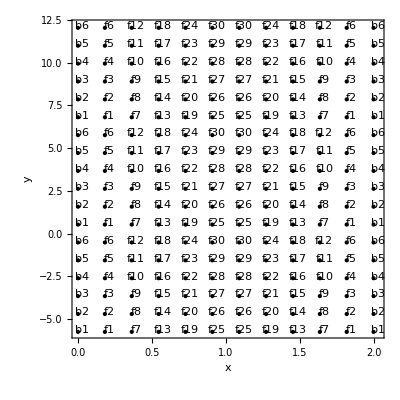

```mathematica
p1=Show[Graphics[Table[Point[gridfull[[ii,1]]],{ii,1,Length[gridfull]}]],PlotRange->All,AspectRatio->1];

p2=Show[Graphics[Table[Text[gridfull[[ii,2]],{0.03,0.1}+gridfull[[ii,1]]],{ii,1,Length[gridfull]}]],PlotRange->All,AspectRatio->1];

Show[p1,p2,Frame->True,FrameLabel->{"x","y"}]
```

## Problem 3 : use ‘Interpolation’ to create finite difference stencil

```mathematica
fninterp=Interpolation[gridfull,InterpolationOrder->2]
```

InterpolatingFunction[{{0., 2.}, {-5.75959, 12.0428}}, <>]

```mathematica
dxfninterp[x_,y_]=D[fninterp[x,y],x];

dyfninterp[x_,y_]=D[fninterp[x,y],y];

dxxfninterp[x_,y_]=D[fninterp[x,y],{x,2}];

dyyfninterp[x_,y_]=D[fninterp[x,y],{y,2}];

dxyfninterp[x_,y_]=D[fninterp[x,y],x,y];
```

```mathematica
fninterp[xval[[ii]],yval[[ii]]]/.{ii->40}//Chop//Quiet
```

InterpolatingFunction[{{0., 2.}, {-5.75959, 12.0428}}, <>][xval⟦40⟧,yval⟦40⟧]

```mathematica
Derivative[1,0][fninterp][xval[[ii]],yval[[ii]]]/.{ii->4}//Chop//Quiet//Simplify//Chop
```

InterpolatingFunction[{{0., 2.}, {-5.75959, 12.0428}}, <>][xval⟦4⟧,yval⟦4⟧]

```mathematica
xval=Table[
grid[[ii,1,1]]
,{ii,1,size}];

yval=Table[
grid[[ii,1,2]]
,{ii,1,size}];

fval=Table[
grid[[ii,2]]
,{ii,1,size}];
```

```mathematica
Print["This takes ",
Timing[

dxfval=Table[
Chop[Simplify[dxfninterp[grid[[ii,1,1]],grid[[ii,1,2]]]]]
,{ii,1,size}];

dyfval=Table[
Chop[Simplify[dyfninterp[grid[[ii,1,1]],grid[[ii,1,2]]]]]
,{ii,1,size}];

dxxfval=Table[
Chop[Simplify[dxxfninterp[grid[[ii,1,1]],grid[[ii,1,2]]]]]
,{ii,1,size}];

dyyfval=Table[
Chop[Simplify[dyyfninterp[grid[[ii,1,1]],grid[[ii,1,2]]]]]
,{ii,1,size}];

dxyfval=Table[
Chop[Simplify[dxyfninterp[grid[[ii,1,1]],grid[[ii,1,2]]]]]
,{ii,1,size}];

][[1]]," seconds to run!"
];
```

This takes 0.16418 seconds to run!

```mathematica
dxfval[[1]]
```

-8.25 b1+11. f1-2.75 f7

Let us check the results;

```mathematica
xval

yval

fval
```

{0.,0.,0.,0.,0.,0.,0.181818,0.181818,0.181818,0.181818,0.181818,0.181818,0.363636,0.363636,0.363636,0.363636,0.363636,0.363636,0.545455,0.545455,0.545455,0.545455,0.545455,0.545455,0.727273,0.727273,0.727273,0.727273,0.727273,0.727273,0.909091,0.909091,0.909091,0.909091,0.909091,0.909091}

{0.523599,1.5708,2.61799,3.66519,4.71239,5.75959,0.523599,1.5708,2.61799,3.66519,4.71239,5.75959,0.523599,1.5708,2.61799,3.66519,4.71239,5.75959,0.523599,1.5708,2.61799,3.66519,4.71239,5.75959,0.523599,1.5708,2.61799,3.66519,4.71239,5.75959,0.523599,1.5708,2.61799,3.66519,4.71239,5.75959}

{b1,b2,b3,b4,b5,b6,f1,f2,f3,f4,f5,f6,f7,f8,f9,f10,f11,f12,f13,f14,f15,f16,f17,f18,f19,f20,f21,f22,f23,f24,f25,f26,f27,f28,f29,f30}

```mathematica
dxfval

dyfval

dxxfval

dyyfval

dxyfval
```

{-8.25 b1+11. f1-2.75 f7,-8.25 b2+11. f2-2.75 f8,-8.25 b3+11. f3-2.75 f9,-8.25 b4-2.75 f10+11. f4,-8.25 b5-2.75 f11+11. f5,-8.25 b6-2.75 f12+11. f6,-2.75 b1+2.75 f7,-2.75 b2+2.75 f8,-2.75 b3+2.75 f9,-2.75 b4+2.75 f10,-2.75 b5+2.75 f11,-2.75 b6+2.75 f12,-2.75 f1+2.75 f13,2.75 f14-2.75 f2,2.75 f15-2.75 f3,2.75 f16-2.75 f4,2.75 f17-2.75 f5,2.75 f18-2.75 f6,2.75 f19-2.75 f7,2.75 f20-2.75 f8,2.75 f21-2.75 f9,-2.75 f10+2.75 f22,-2.75 f11+2.75 f23,-2.75 f12+2.75 f24,-2.75 f13+2.75 f25,-2.75 f14+2.75 f26,-2.75 f15+2.75 f27,-2.75 f16+2.75 f28,-2.75 f17+2.75 f29,-2.75 f18+2.75 f30,-2.75 f19+2.75 f25,-2.75 f20+2.75 f26,-2.75 f21+2.75 f27,-2.75 f22+2.75 f28,-2.75 f23+2.75 f29,-2.75 f24+2.75 f30}

{0.477465 b2-0.477465 b6,-0.477465 b1+0.477465 b3,-0.477465 b2+0.477465 b4,-0.477465 b3+0.477465 b5,-0.477465 b4+0.477465 b6,0.477465 b1-0.477465 b5,0.477465 f2-0.477465 f6,-0.477465 f1+0.477465 f3,-0.477465 f2+0.477465 f4,-0.477465 f3+0.477465 f5,-0.477465 f4+0.477465 f6,0.477465 f1-0.477465 f5,-0.477465 f12+0.477465 f8,-0.477465 f7+0.477465 f9,0.477465 f10-0.477465 f8,0.477465 f11-0.477465 f9,-0.477465 f10+0.477465 f12,-0.477465 f11+0.477465 f7,0.477465 f14-0.477465 f18,-0.477465 f13+0.477465 f15,-0.477465 f14+0.477465 f16,-0.477465 f15+0.477465 f17,-0.477465 f16+0.477465 f18,0.477465 f13-0.477465 f17,0.477465 f20-0.477465 f24,-0.477465 f19+0.477465 f21,-0.477465 f20+0.477465 f22,-0.477465 f21+0.477465 f23,-0.477465 f22+0.477465 f24,0.477465 f19-0.477465 f23,0.477465 f26-0.477465 f30,-0.477465 f25+0.477465 f27,-0.477465 f26+0.477465 f28,-0.477465 f27+0.477465 f29,-0.477465 f28+0.477465 f30,0.477465 f25-0.477465 f29}

{30.25 b1-60.5 f1+30.25 f7,30.25 b2-60.5 f2+30.25 f8,30.25 b3-60.5 f3+30.25 f9,30.25 b4+30.25 f10-60.5 f4,30.25 b5+30.25 f11-60.5 f5,30.25 b6+30.25 f12-60.5 f6,30.25 b1-60.5 f1+30.25 f7,30.25 b2-60.5 f2+30.25 f8,30.25 b3-60.5 f3+30.25 f9,30.25 b4+30.25 f10-60.5 f4,30.25 b5+30.25 f11-60.5 f5,30.25 b6+30.25 f12-60.5 f6,30.25 f1+30.25 f13-60.5 f7,30.25 f14+30.25 f2-60.5 f8,30.25 f15+30.25 f3-60.5 f9,-60.5 f10+30.25 f16+30.25 f4,-60.5 f11+30.25 f17+30.25 f5,-60.5 f12+30.25 f18+30.25 f6,-60.5 f13+30.25 f19+30.25 f7,-60.5 f14+30.25 f20+30.25 f8,-60.5 f15+30.25 f21+30.25 f9,30.25 f10-60.5 f16+30.25 f22,30.25 f11-60.5 f17+30.25 f23,30.25 f12-60.5 f18+30.25 f24,30.25 f13-60.5 f19+30.25 f25,30.25 f14-60.5 f20+30.25 f26,30.25 f15-60.5 f21+30.25 f27,30.25 f16-60.5 f22+30.25 f28,30.25 f17-60.5 f23+30.25 f29,30.25 f18-60.5 f24+30.25 f30,30.25 f19-30.25 f25,30.25 f20-30.25 f26,30.25 f21-30.25 f27,30.25 f22-30.25 f28,30.25 f23-30.25 f29,30.25 f24-30.25 f30}

{-1.82378 b1+0.911891 b2+0.911891 b6,0.911891 b1-1.82378 b2+0.911891 b3,0.911891 b2-1.82378 b3+0.911891 b4,0.911891 b3-1.82378 b4+0.911891 b5,0.911891 b4-1.82378 b5+0.911891 b6,0.911891 b1+0.911891 b5-1.82378 b6,-1.82378 f1+0.911891 f2+0.911891 f6,0.911891 f1-1.82378 f2+0.911891 f3,0.911891 f2-1.82378 f3+0.911891 f4,0.911891 f3-1.82378 f4+0.911891 f5,0.911891 f4-1.82378 f5+0.911891 f6,0.911891 f1+0.911891 f5-1.82378 f6,0.911891 f12-1.82378 f7+0.911891 f8,0.911891 f7-1.82378 f8+0.911891 f9,0.911891 f10+0.911891 f8-1.82378 f9,-1.82378 f10+0.911891 f11+0.911891 f9,0.911891 f10-1.82378 f11+0.911891 f12,0.911891 f11-1.82378 f12+0.911891 f7,-1.82378 f13+0.911891 f14+0.911891 f18,0.911891 f13-1.82378 f14+0.911891 f15,0.911891 f14-1.82378 f15+0.911891 f16,0.911891 f15-1.82378 f16+0.911891 f17,0.911891 f16-1.82378 f17+0.911891 f18,0.911891 f13+0.911891 f17-1.82378 f18,-1.82378 f19+0.911891 f20+0.911891 f24,0.911891 f19-1.82378 f20+0.911891 f21,0.911891 f20-1.82378 f21+0.911891 f22,0.911891 f21-1.82378 f22+0.911891 f23,0.911891 f22-1.82378 f23+0.911891 f24,0.911891 f19+0.911891 f23-1.82378 f24,-1.82378 f25+0.911891 f26+0.911891 f30,0.911891 f25-1.82378 f26+0.911891 f27,0.911891 f26-1.82378 f27+0.911891 f28,0.911891 f27-1.82378 f28+0.911891 f29,0.911891 f28-1.82378 f29+0.911891 f30,0.911891 f25+0.911891 f29-1.82378 f30}

{-3.93908 b2+3.93908 b6+1.31303 f12+5.25211 f2-5.25211 f6-1.31303 f8,3.93908 b1-3.93908 b3-5.25211 f1+5.25211 f3+1.31303 f7-1.31303 f9,3.93908 b2-3.93908 b4-1.31303 f10-5.25211 f2+5.25211 f4+1.31303 f8,3.93908 b3-3.93908 b5-1.31303 f11-5.25211 f3+5.25211 f5+1.31303 f9,3.93908 b4-3.93908 b6+1.31303 f10-1.31303 f12-5.25211 f4+5.25211 f6,-3.93908 b1+3.93908 b5+5.25211 f1+1.31303 f11-5.25211 f5-1.31303 f7,-1.31303 b2+1.31303 b6-1.31303 f12+1.31303 f8,1.31303 b1-1.31303 b3-1.31303 f7+1.31303 f9,1.31303 b2-1.31303 b4+1.31303 f10-1.31303 f8,1.31303 b3-1.31303 b5+1.31303 f11-1.31303 f9,1.31303 b4-1.31303 b6-1.31303 f10+1.31303 f12,-1.31303 b1+1.31303 b5-1.31303 f11+1.31303 f7,1.31303 f14-1.31303 f18-1.31303 f2+1.31303 f6,1.31303 f1-1.31303 f13+1.31303 f15-1.31303 f3,-1.31303 f14+1.31303 f16+1.31303 f2-1.31303 f4,-1.31303 f15+1.31303 f17+1.31303 f3-1.31303 f5,-1.31303 f16+1.31303 f18+1.31303 f4-1.31303 f6,-1.31303 f1+1.31303 f13-1.31303 f17+1.31303 f5,1.31303 f12+1.31303 f20-1.31303 f24-1.31303 f8,-1.31303 f19+1.31303 f21+1.31303 f7-1.31303 f9,-1.31303 f10-1.31303 f20+1.31303 f22+1.31303 f8,-1.31303 f11-1.31303 f21+1.31303 f23+1.31303 f9,1.31303 f10-1.31303 f12-1.31303 f22+1.31303 f24,1.31303 f11+1.31303 f19-1.31303 f23-1.31303 f7,-1.31303 f14+1.31303 f18+1.31303 f26-1.31303 f30,1.31303 f13-1.31303 f15-1.31303 f25+1.31303 f27,1.31303 f14-1.31303 f16-1.31303 f26+1.31303 f28,1.31303 f15-1.31303 f17-1.31303 f27+1.31303 f29,1.31303 f16-1.31303 f18-1.31303 f28+1.31303 f30,-1.31303 f13+1.31303 f17+1.31303 f25-1.31303 f29,-1.31303 f20+1.31303 f24+1.31303 f26-1.31303 f30,1.31303 f19-1.31303 f21-1.31303 f25+1.31303 f27,1.31303 f20-1.31303 f22-1.31303 f26+1.31303 f28,1.31303 f21-1.31303 f23-1.31303 f27+1.31303 f29,1.31303 f22-1.31303 f24-1.31303 f28+1.31303 f30,-1.31303 f19+1.31303 f23+1.31303 f25-1.31303 f29}

## Problem 4 : check our discretization

```mathematica
fn[x_,y_]=Cos[y](1-0.5(1-x)^2);
```

```mathematica
fnx[x_,y_]=D[fn[x,y],x];

fny[x_,y_]=D[fn[x,y],y];

fnxx[x_,y_]=D[fn[x,y],{x,2}];

fnyy[x_,y_]=D[fn[x,y],{y,2}];

fnxy[x_,y_]=D[fn[x,y],x,y];
```

```mathematica
varrepl=Thread[variables->Table[
fn[grid[[ii,1,1]],grid[[ii,1,2]]]
,{ii,1,size}]]
```

{b1→0.433013,b2→3.06162×10^-17,b3→-0.433013,b4→-0.433013,b5→-9.18485×10^-17,b6→0.433013,f1→0.576157,f2→4.07372×10^-17,f3→-0.576157,f4→-0.576157,f5→-1.22212×10^-16,f6→0.576157,f7→0.690673,f8→4.88341×10^-17,f9→-0.690673,f10→-0.690673,f11→-1.46502×10^-16,f12→0.690673,f13→0.77656,f14→5.49067×10^-17,f15→-0.77656,f16→-0.77656,f17→-1.6472×10^-16,f18→0.77656,f19→0.833818,f20→5.89551×10^-17,f21→-0.833818,f22→-0.833818,f23→-1.76865×10^-16,f24→0.833818,f25→0.862447,f26→6.09793×10^-17,f27→-0.862447,f28→-0.862447,f29→-1.82938×10^-16,f30→0.862447}

Check our discretized x derivatives; since we used 2nd order polynominal interpolation and fn is only quadratic in x this should agree (up to numerical precision).

```mathematica
Table[fnx[x,y]/.{x->xval[[ii]],y->yval[[ii]]},{ii,1,Length[xval]}]
```

{0.866025,6.12323×10^-17,-0.866025,-0.866025,-1.83697×10^-16,0.866025,0.708566,5.00992×10^-17,-0.708566,-0.708566,-1.50298×10^-16,0.708566,0.551107,3.8966×10^-17,-0.551107,-0.551107,-1.16898×10^-16,0.551107,0.393648,2.78329×10^-17,-0.393648,-0.393648,-8.34986×10^-17,0.393648,0.236189,1.66997×10^-17,-0.236189,-0.236189,-5.00992×10^-17,0.236189,0.0787296,5.56658×10^-18,-0.0787296,-0.0787296,-1.66997×10^-17,0.0787296}

```mathematica
dxfval/.varrepl
```

{0.866025,6.12323×10^-17,-0.866025,-0.866025,-1.83697×10^-16,0.866025,0.708566,5.00992×10^-17,-0.708566,-0.708566,-1.50298×10^-16,0.708566,0.551107,3.8966×10^-17,-0.551107,-0.551107,-1.16898×10^-16,0.551107,0.393648,2.78329×10^-17,-0.393648,-0.393648,-8.34986×10^-17,0.393648,0.236189,1.66997×10^-17,-0.236189,-0.236189,-5.00992×10^-17,0.236189,0.0787296,5.56658×10^-18,-0.0787296,-0.0787296,-1.66997×10^-17,0.0787296}

Let' s plot these results;

```mathematica
ListPlot3D[Table[
{grid[[ii,1,1]],grid[[ii,1,2]],dxfval[[ii]]/.varrepl}
,{ii,1,size}]]

ListPlot3D[Table[
{grid[[ii,1,1]],grid[[ii,1,2]],(dxfval[[ii]]/.varrepl)-fnx[grid[[ii,1,1]],grid[[ii,1,2]]]}
,{ii,1,size}]]
```

-Graphics3D-

-Graphics3D-

Let’s do the same for the discretized y derivatives; now we shouldn’t see exact agreement. In fact for low resolution we shouldn’t see very good agreement; go back and rerun this for NX=NY=10 and InterpolationOrder->6 and you should see a much better agreement.

```mathematica
Table[fny[x,y]/.{x->xval[[ii]],y->yval[[ii]]},{ii,1,Length[xval]}]
```

{-0.25,-0.5,-0.25,0.25,0.5,0.25,-0.332645,-0.665289,-0.332645,0.332645,0.665289,0.332645,-0.39876,-0.797521,-0.39876,0.39876,0.797521,0.39876,-0.448347,-0.896694,-0.448347,0.448347,0.896694,0.448347,-0.481405,-0.96281,-0.481405,0.481405,0.96281,0.481405,-0.497934,-0.995868,-0.497934,0.497934,0.995868,0.497934}

```mathematica
dyfval/.varrepl
```

{-0.206748,-0.413497,-0.206748,0.206748,0.413497,0.206748,-0.275095,-0.55019,-0.275095,0.275095,0.55019,0.275095,-0.329772,-0.659544,-0.329772,0.329772,0.659544,0.329772,-0.37078,-0.74156,-0.37078,0.37078,0.74156,0.37078,-0.398119,-0.796237,-0.398119,0.398119,0.796237,0.398119,-0.411788,-0.823576,-0.411788,0.411788,0.823576,0.411788}

Let' s plot these results;

```mathematica
ListPlot3D[Table[
{grid[[ii,1,1]],grid[[ii,1,2]],dyfval[[ii]]/.varrepl}
,{ii,1,size}]]

ListPlot3D[Table[
{grid[[ii,1,1]],grid[[ii,1,2]],(dyfval[[ii]]/.varrepl)-fny[grid[[ii,1,1]],grid[[ii,1,2]]]}
,{ii,1,size}]]
```

-Graphics3D-

-Graphics3D-

## Problem 5 : implement boundary conditions, initial guess and p.d.e. to be solved.

```mathematica
bfn[x_,y_]=Cos[y];
```

This code creates the boundary and interior replacelists for the boundary condition at x=0 and the initial guess for the interior points respectively. Note that we are using the lists ' boundary' and ' interior' that we created initially when we built ' grid'.

```mathematica
boundaryrepl=Thread[boundaryvar->Table[
bfn[grid[[boundary[[ii]],1,1]],grid[[boundary[[ii]],1,2]]]
,{ii,1,sizeboundary}]]

interiorrepl=Thread[interiorvar->Table[
bfn[grid[[interior[[ii]],1,1]],grid[[interior[[ii]],1,2]]]
,{ii,1,sizeinterior}]]
```

{b1→0.866025,b2→6.12323×10^-17,b3→-0.866025,b4→-0.866025,b5→-1.83697×10^-16,b6→0.866025}

{f1→0.866025,f2→6.12323×10^-17,f3→-0.866025,f4→-0.866025,f5→-1.83697×10^-16,f6→0.866025,f7→0.866025,f8→6.12323×10^-17,f9→-0.866025,f10→-0.866025,f11→-1.83697×10^-16,f12→0.866025,f13→0.866025,f14→6.12323×10^-17,f15→-0.866025,f16→-0.866025,f17→-1.83697×10^-16,f18→0.866025,f19→0.866025,f20→6.12323×10^-17,f21→-0.866025,f22→-0.866025,f23→-1.83697×10^-16,f24→0.866025,f25→0.866025,f26→6.12323×10^-17,f27→-0.866025,f28→-0.866025,f29→-1.83697×10^-16,f30→0.866025}

Now creating the equation list at the interior points is very straightforward (where we also impose the boundary condition at x=0 using boundaryrepl)

```mathematica
interiorequations=Table[
(dxxfval+5dyyfval)[[interior[[ii]]]]/.boundaryrepl
,{ii,1,sizeinterior}]
```

{26.1973-60.5 f1+5 (-1.82378 f1+0.911891 f2+0.911891 f6)+30.25 f7,1.85228×10^-15-60.5 f2+5 (0.911891 f1-1.82378 f2+0.911891 f3)+30.25 f8,-26.1973-60.5 f3+5 (0.911891 f2-1.82378 f3+0.911891 f4)+30.25 f9,-26.1973+30.25 f10-60.5 f4+5 (0.911891 f3-1.82378 f4+0.911891 f5),-5.55683×10^-15+30.25 f11-60.5 f5+5 (0.911891 f4-1.82378 f5+0.911891 f6),26.1973+30.25 f12+5 (0.911891 f1+0.911891 f5-1.82378 f6)-60.5 f6,30.25 f1+30.25 f13-60.5 f7+5 (0.911891 f12-1.82378 f7+0.911891 f8),30.25 f14+30.25 f2-60.5 f8+5 (0.911891 f7-1.82378 f8+0.911891 f9),30.25 f15+30.25 f3+5 (0.911891 f10+0.911891 f8-1.82378 f9)-60.5 f9,-60.5 f10+30.25 f16+30.25 f4+5 (-1.82378 f10+0.911891 f11+0.911891 f9),-60.5 f11+5 (0.911891 f10-1.82378 f11+0.911891 f12)+30.25 f17+30.25 f5,-60.5 f12+30.25 f18+30.25 f6+5 (0.911891 f11-1.82378 f12+0.911891 f7),-60.5 f13+5 (-1.82378 f13+0.911891 f14+0.911891 f18)+30.25 f19+30.25 f7,-60.5 f14+5 (0.911891 f13-1.82378 f14+0.911891 f15)+30.25 f20+30.25 f8,-60.5 f15+5 (0.911891 f14-1.82378 f15+0.911891 f16)+30.25 f21+30.25 f9,30.25 f10-60.5 f16+5 (0.911891 f15-1.82378 f16+0.911891 f17)+30.25 f22,30.25 f11-60.5 f17+5 (0.911891 f16-1.82378 f17+0.911891 f18)+30.25 f23,30.25 f12+5 (0.911891 f13+0.911891 f17-1.82378 f18)-60.5 f18+30.25 f24,30.25 f13-60.5 f19+5 (-1.82378 f19+0.911891 f20+0.911891 f24)+30.25 f25,30.25 f14-60.5 f20+5 (0.911891 f19-1.82378 f20+0.911891 f21)+30.25 f26,30.25 f15-60.5 f21+5 (0.911891 f20-1.82378 f21+0.911891 f22)+30.25 f27,30.25 f16-60.5 f22+5 (0.911891 f21-1.82378 f22+0.911891 f23)+30.25 f28,30.25 f17-60.5 f23+5 (0.911891 f22-1.82378 f23+0.911891 f24)+30.25 f29,30.25 f18+5 (0.911891 f19+0.911891 f23-1.82378 f24)-60.5 f24+30.25 f30,30.25 f19-30.25 f25+5 (-1.82378 f25+0.911891 f26+0.911891 f30),30.25 f20-30.25 f26+5 (0.911891 f25-1.82378 f26+0.911891 f27),30.25 f21-30.25 f27+5 (0.911891 f26-1.82378 f27+0.911891 f28),30.25 f22-30.25 f28+5 (0.911891 f27-1.82378 f28+0.911891 f29),30.25 f23-30.25 f29+5 (0.911891 f28-1.82378 f29+0.911891 f30),30.25 f24+5 (0.911891 f25+0.911891 f29-1.82378 f30)-30.25 f30}

## Problem 6 : Solve the Laplace equation

```mathematica
varandguess=Transpose[Partition[Join[interiorvar,interiorvar/.interiorrepl],sizeinterior]]
```

{{f1,0.866025},{f2,6.12323×10^-17},{f3,-0.866025},{f4,-0.866025},{f5,-1.83697×10^-16},{f6,0.866025},{f7,0.866025},{f8,6.12323×10^-17},{f9,-0.866025},{f10,-0.866025},{f11,-1.83697×10^-16},{f12,0.866025},{f13,0.866025},{f14,6.12323×10^-17},{f15,-0.866025},{f16,-0.866025},{f17,-1.83697×10^-16},{f18,0.866025},{f19,0.866025},{f20,6.12323×10^-17},{f21,-0.866025},{f22,-0.866025},{f23,-1.83697×10^-16},{f24,0.866025},{f25,0.866025},{f26,6.12323×10^-17},{f27,-0.866025},{f28,-0.866025},{f29,-1.83697×10^-16},{f30,0.866025}}

```mathematica
FindRoot[interiorequations,varandguess]
```

{f1→0.598484,f2→3.5607×10^-17,f3→-0.598484,f4→-0.598484,f5→-9.08034×10^-17,f6→0.598484,f7→0.421149,f8→2.94193×10^-17,f9→-0.421149,f10→-0.421149,f11→-3.25682×10^-17,f12→0.421149,f13→0.307292,f14→1.03376×10^-17,f15→-0.307292,f16→-0.307292,f17→2.97637×10^-18,f18→0.307292,f19→0.239752,f20→-8.39065×10^-18,f21→-0.239752,f22→-0.239752,f23→2.53014×10^-17,f24→0.239752,f25→0.208348,f26→-3.32832×10^-17,f27→-0.208348,f28→-0.208348,f29→6.01165×10^-17,f30→0.208348}

```mathematica
Norm[interiorequations/.interiorrepl]
```

17.6587

```mathematica
solution=FindRoot[interiorequations,varandguess,StepMonitor:>Print["norm = ",Norm[interiorequations]]]
```

norm = 2.34418×10^-14

{f1→0.598484,f2→3.5607×10^-17,f3→-0.598484,f4→-0.598484,f5→-9.08034×10^-17,f6→0.598484,f7→0.421149,f8→2.94193×10^-17,f9→-0.421149,f10→-0.421149,f11→-3.25682×10^-17,f12→0.421149,f13→0.307292,f14→1.03376×10^-17,f15→-0.307292,f16→-0.307292,f17→2.97637×10^-18,f18→0.307292,f19→0.239752,f20→-8.39065×10^-18,f21→-0.239752,f22→-0.239752,f23→2.53014×10^-17,f24→0.239752,f25→0.208348,f26→-3.32832×10^-17,f27→-0.208348,f28→-0.208348,f29→6.01165×10^-17,f30→0.208348}

```mathematica
ListPlot3D[Table[
{grid[[ii,1,1]],grid[[ii,1,2]],fval[[ii]]/.boundaryrepl/.solution}
,{ii,1,Length[grid]}],PlotRange->All]
```

-Graphics3D-

```mathematica
p1=ListPointPlot3D[Table[
{grid[[ii,1,1]],grid[[ii,1,2]],fval[[ii]]/.boundaryrepl/.solution}
,{ii,1,Length[grid]}],PlotRange->All];

p2=ListPlot3D[Table[
{grid[[ii,1,1]],grid[[ii,1,2]],fval[[ii]]/.boundaryrepl/.solution}
,{ii,1,Length[grid]}],PlotRange->All,Mesh->False];

Show[p1,p2]
```

-Graphics3D-

```mathematica
disp[x_]:=Block[{p1,p2},

p1=ListPointPlot3D[x,PlotRange->All];

p2=ListPlot3D[x,PlotRange->All,Mesh->False];

Print[Show[p1,p2]];

]
```

```mathematica
disp[
Table[
{grid[[ii,1,1]],grid[[ii,1,2]],fval[[ii]]/.boundaryrepl/.solution}
,{ii,1,Length[grid]}]
]
```

-Graphics3D-

The exact analytic solution for these boundary conditions is;

```mathematica
f[x_,y_]:=Cos[y] Cosh[Sqrt[5](x-1)]/Cosh[Sqrt[5]]
```

```mathematica
Simplify[D[f[x, y], {x, 2}] + 5 D[f[x, y], {y, 2}]]

Simplify[f[0,y]]
```

0

Cos[y]

```mathematica
ListPlot3D[Table[
{grid[[ii,1,1]],grid[[ii,1,2]],f[grid[[ii,1,1]],grid[[ii,1,2]]]}
,{ii,1,Length[grid]}],PlotRange->All]
```

-Graphics3D-

The difference with our discrete solution is;

```mathematica
disp[Table[
{grid[[ii,1,1]],grid[[ii,1,2]],(fval[[ii]]/.boundaryrepl/.solution)-f[grid[[ii,1,1]],grid[[ii,1,2]]]},{ii,1,Length[grid]}]]
```

-Graphics3D-

## Problem 7 : Solve a non-linear Laplace equation

```mathematica
interiorequations=Table[
(dxxfval+5dyyfval-2fval^2)[[interior[[ii]]]]/.boundaryrepl
,{ii,1,sizeinterior}];
```

```mathematica
solution2=FindRoot[interiorequations,varandguess,StepMonitor:>Print["Step; norm = ",Norm[interiorequations]]]
```

Step; norm = 5.95388

Step; norm = 0.951539

Step; norm = 0.0647053

Step; norm = 0.000423967

Step; norm = 1.90375×10^-8

Step; norm = 2.22145×10^-14

{f1→0.563852,f2→-0.0233943,f3→-0.645467,f4→-0.645467,f5→-0.0233943,f6→0.563852,f7→0.371211,f8→-0.0415032,f9→-0.491126,f10→-0.491126,f11→-0.0415032,f12→0.371211,f13→0.249887,f14→-0.053935,f15→-0.388606,f16→-0.388606,f17→-0.053935,f18→0.249887,f19→0.178486,f20→-0.0615248,f21→-0.326546,f22→-0.326546,f23→-0.0615248,f24→0.178486,f25→0.145367,f26→-0.0650947,f27→-0.297382,f28→-0.297382,f29→-0.0650947,f30→0.145367}

```mathematica
ListPlot3D[Table[
{grid[[ii,1,1]],grid[[ii,1,2]],fval[[ii]]/.boundaryrepl/.solution2}
,{ii,1,size}],PlotRange->All]
```

-Graphics3D-

## ***NEW section*** Illustration of Newton’s method

```mathematica
Δ=10^-3;
```

```mathematica
LinOp[data_]:=Table[

dataup=data;

datadown=data;

dataup[[ii]]+=Δ;datadown[[ii]]-=Δ;

((interiorequations/.Thread[interiorvar->dataup])-(interiorequations/.Thread[interiorvar->datadown]))/(2Δ)

,{ii,1,Length[data]}];
```

```mathematica
sol=interiorvar/.interiorrepl
```

{0.866025,6.12323×10^-17,-0.866025,-0.866025,-1.83697×10^-16,0.866025,0.866025,6.12323×10^-17,-0.866025,-0.866025,-1.83697×10^-16,0.866025,0.866025,6.12323×10^-17,-0.866025,-0.866025,-1.83697×10^-16,0.866025,0.866025,6.12323×10^-17,-0.866025,-0.866025,-1.83697×10^-16,0.866025,0.866025,6.12323×10^-17,-0.866025,-0.866025,-1.83697×10^-16,0.866025}

```mathematica
Do[

equationvalues=(interiorequations/.Thread[interiorvar->sol]);

sol-=LinearSolve[Transpose[LinOp[sol]],equationvalues];

Print[Norm[equationvalues]];

,{iter,1,5}]
```

18.8899

5.95388

0.951539

0.0647053

0.000423967

```mathematica
Thread[interiorvar->sol]
```

{f1→0.563852,f2→-0.0233943,f3→-0.645467,f4→-0.645467,f5→-0.0233943,f6→0.563852,f7→0.371211,f8→-0.0415032,f9→-0.491126,f10→-0.491126,f11→-0.0415032,f12→0.371211,f13→0.249887,f14→-0.053935,f15→-0.388606,f16→-0.388606,f17→-0.053935,f18→0.249887,f19→0.178486,f20→-0.0615248,f21→-0.326546,f22→-0.326546,f23→-0.0615248,f24→0.178486,f25→0.145367,f26→-0.0650947,f27→-0.297382,f28→-0.297382,f29→-0.0650947,f30→0.145367}